```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

```mathematica
misfit[ϵ1_,x_,y_,σ_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},lista={{imp8,imp8,imp6,imp5,imp12,imp7,imp9,imp14,imp4,imp8,imp11,imp11,imp14,imp6,imp12,imp14,imp12,imp2,imp6,imp10,imp7,imp1,imp3,imp10,imp6,imp8,imp13,imp10,imp,imp3,imp13,imp2,imp9,imp5,imp9,imp14,imp8,imp7,imp13,imp2,imp1,imp4,imp3,imp5,imp3,imp11,imp2,imp5,imp6,imp5,imp13,imp7,imp9,imp5,imp1,imp4,imp12,imp13,imp13,imp11,imp,imp8,imp10,imp1,imp13,imp3,imp6,imp2,imp12,imp4,imp4,imp10,imp5,imp14,imp14,imp2,imp11,imp2,imp10,imp3,imp14,imp9,imp12,imp7,imp1,imp4,imp7,imp11,imp7,imp6,imp1,imp1,imp9,imp10,imp8,imp11,imp12,imp9,imp3,imp4}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ11:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/140imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ12:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],Abs[m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/156imp100.csv"][[1;;300,;;]][[;;,2]]]^σ}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
list={ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10,ρ11,ρ12};list];
υ]
```

```mathematica
aa=ParallelTable[misfit[0.5,0,1.2,2],100]
```

{{0.00845932,0.00405948,0.00230263,0.00155084,0.00123408,0.00110771,0.00107619,0.00122041,0.00129531,0.00138683,0.00147106},{0.00819811,0.00402001,0.00233892,0.00161265,0.00126661,0.00112879,0.00108444,0.00117333,0.00124952,0.00133164,0.00141627},{0.00738961,0.00360342,0.00217059,0.0016258,0.00143429,0.00142853,0.00150368,0.00174613,0.00186223,0.00197641,0.00208987},{0.00881462,0.00449497,0.00269637,0.00187844,0.00145848,0.00127117,0.00117649,0.00123473,0.00129441,0.00136853,0.00145942},{0.00814065,0.00401883,0.00230216,0.00156213,0.00124239,0.00111058,0.00107885,0.00119629,0.00129663,0.00141122,0.00153403},{0.00848054,0.00411418,0.00228766,0.001506,0.0012026,0.00112646,0.00115337,0.00125874,0.00134715,0.00145047,0.00153903},{0.00824329,0.00401845,0.00228193,0.00152827,0.00119583,0.00109671,0.00110817,0.00123446,0.00132995,0.00142947,0.00152569},{0.00781191,0.00395739,0.00244185,0.00185024,0.0016341,0.00158035,0.00158654,0.00170314,0.00178936,0.00187654,0.00196861},{0.00868633,0.00422223,0.00234022,0.00150781,0.00117125,0.00108471,0.00110568,0.00120917,0.00129807,0.00141019,0.00151134},{0.00752897,0.00351238,0.00196115,0.00136385,0.00113705,0.00109999,0.0011286,0.00131886,0.00142319,0.00153561,0.00164953},{0.00894548,0.00466821,0.0028738,0.00206896,0.00171548,0.00158575,0.00158957,0.00171467,0.0018052,0.00190802,0.00202069},{0.00794674,0.00400728,0.00248567,0.00185192,0.00156927,0.00148816,0.0014856,0.00161843,0.00171481,0.00180346,0.00190213},{0.00718187,0.00321342,0.00170153,0.00111508,0.000905433,0.000905299,0.00102214,0.00128556,0.00143333,0.00156402,0.00168878},{0.00529383,0.00225455,0.00128771,0.00109388,0.00120743,0.00143129,0.00175255,0.00225046,0.00249877,0.00272764,0.00293368},{0.00709785,0.00336601,0.00191704,0.00133906,0.00111101,0.00105612,0.00107445,0.00127834,0.00137246,0.00147145,0.00157383},{0.00710363,0.00348006,0.00208342,0.00152837,0.00133879,0.00131207,0.00136105,0.00158209,0.001716,0.00186172,0.00201463},{0.00762387,0.00352934,0.001937,0.00127334,0.000984104,0.00091397,0.000961967,0.00113149,0.00124187,0.00134767,0.00146677},{0.00908238,0.00498539,0.00325182,0.00241913,0.00197961,0.0017161,0.0015555,0.00156653,0.0016111,0.00169671,0.0017939},{0.00827074,0.00421558,0.00259325,0.00186249,0.00152801,0.00137431,0.00128923,0.00133578,0.0013943,0.00145663,0.00153057},{0.00866724,0.00456128,0.00284232,0.00205287,0.00166876,0.00150899,0.00144519,0.00139854,0.00142186,0.00146788,0.0015119},{0.00750908,0.0035062,0.00197288,0.0013761,0.00114585,0.00110468,0.00112974,0.00133247,0.00143324,0.00152438,0.00162372},{0.00818012,0.00397049,0.00224631,0.0014985,0.00116542,0.00107475,0.00111588,0.00125352,0.00135886,0.00147015,0.0015806},{0.0086757,0.00444728,0.0026398,0.00181768,0.00140606,0.00122218,0.00114522,0.00117747,0.00125339,0.00133102,0.0014239},{0.00794,0.00401444,0.00250078,0.00187665,0.00157979,0.00145284,0.0014091,0.00150831,0.00156411,0.00162017,0.00170373},{0.00811956,0.00402297,0.00240431,0.00168829,0.00136649,0.00125246,0.00123434,0.00136063,0.00141895,0.00149577,0.00157539},{0.00815794,0.00416782,0.00254061,0.00181877,0.00147819,0.00138851,0.00142337,0.0015719,0.00167206,0.00179689,0.0019084},{0.00810853,0.00395304,0.00225843,0.00151508,0.00119638,0.00105041,0.00102487,0.00107004,0.00111572,0.00117532,0.00123106},{0.00863183,0.00456134,0.00288234,0.00212176,0.00175296,0.00157668,0.00150729,0.00155886,0.00163864,0.00172587,0.00182586},{0.00681298,0.00319914,0.00188278,0.00140555,0.00122976,0.00120074,0.00124557,0.00146194,0.00158098,0.00170135,0.00184129},{0.00825475,0.00387214,0.00207872,0.00129284,0.00095654,0.000830423,0.000825267,0.000911332,0.00097889,0.00105499,0.00112522},{0.00692668,0.00303195,0.00157066,0.00101622,0.000813239,0.000795406,0.000850962,0.00104647,0.00113948,0.00123504,0.0013315},{0.00804346,0.00394172,0.00230056,0.00158804,0.00126964,0.00116418,0.0011486,0.00123494,0.00129895,0.00137314,0.00145118},{0.00625115,0.00283592,0.00167151,0.00131867,0.00125902,0.00133952,0.0014712,0.00176907,0.00189284,0.002021,0.00214101},{0.00835017,0.00419937,0.00249392,0.00170638,0.00130779,0.00110395,0.00100936,0.00101707,0.00106509,0.00113369,0.0012037},{0.00830764,0.00407579,0.00231265,0.00151428,0.0011293,0.000967467,0.000911454,0.00100152,0.00109786,0.00121024,0.00132456},{0.00706444,0.00331939,0.00192196,0.00140647,0.00121208,0.0012194,0.00131879,0.00159423,0.00172215,0.00184805,0.00196901},{0.00610531,0.00262148,0.00150738,0.00119646,0.00118787,0.00131571,0.00151647,0.00191873,0.00208533,0.00223655,0.00236992},{0.00871079,0.00443348,0.00260878,0.00176124,0.00135235,0.0011555,0.00106085,0.00110556,0.00115412,0.00124011,0.00131984},{0.00753483,0.00373427,0.00222882,0.00161542,0.00140992,0.00138193,0.00144594,0.00164559,0.00176935,0.00190229,0.00202971},{0.00861153,0.00416437,0.00233246,0.00148855,0.00111123,0.000940402,0.000869099,0.000864656,0.000904914,0.000968761,0.00103093},{0.00768356,0.00371409,0.00219326,0.00158453,0.00133277,0.00125291,0.00123486,0.00132573,0.00139957,0.00146147,0.00153313},{0.00896184,0.00439675,0.00244557,0.00155428,0.0011544,0.00101479,0.000986567,0.0010702,0.00114377,0.001228,0.0013083},{0.00916883,0.00470931,0.00277772,0.00185785,0.00135284,0.00110222,0.000945216,0.000929081,0.000947038,0.000997887,0.00105515},{0.00726492,0.00345268,0.00196723,0.0013546,0.00110216,0.00101059,0.000987718,0.00111238,0.00120766,0.00131284,0.00141471},{0.00816923,0.00412215,0.00241984,0.00161453,0.00117209,0.000973139,0.000890759,0.000958392,0.00102738,0.00109842,0.00118078},{0.0073631,0.00325042,0.00172787,0.00119611,0.00104317,0.00105823,0.00115902,0.0013745,0.00150713,0.00164977,0.00178022},{0.00815501,0.00398772,0.00225219,0.00146701,0.00107925,0.000920451,0.000857873,0.000903057,0.00096759,0.0010345,0.00111681},{0.00753404,0.00384439,0.00243424,0.00184938,0.00157993,0.00149649,0.00147537,0.00160666,0.00169142,0.00177645,0.0018733},{0.00808324,0.00385692,0.00216987,0.00144101,0.00110057,0.00097995,0.000961739,0.0010628,0.00113507,0.00122005,0.00131302},{0.00630191,0.00295402,0.00178436,0.00142313,0.00135097,0.00140151,0.0015635,0.00191029,0.00207632,0.00223879,0.00239141},{0.00763611,0.00392592,0.00240716,0.00170937,0.00135762,0.00119012,0.00116659,0.00131612,0.00141022,0.00151672,0.00162642},{0.00782592,0.00359308,0.00189933,0.00118624,0.00088753,0.000812816,0.000837875,0.000956014,0.00104458,0.00115147,0.0012538},{0.00620973,0.00264612,0.00143747,0.00109329,0.00106313,0.00119845,0.00141492,0.0018496,0.00206604,0.00226793,0.00247049},{0.00856232,0.00424049,0.00247429,0.00169195,0.00131091,0.0011309,0.00103479,0.00105289,0.00109104,0.00112404,0.00117562},{0.00787353,0.00360975,0.00192759,0.0012609,0.00100852,0.000988681,0.00106592,0.00127484,0.00139378,0.00152322,0.00163531},{0.00856658,0.00426276,0.00250791,0.00172284,0.00133383,0.00115519,0.00106438,0.00113303,0.00117551,0.00124128,0.0013101},{0.00722802,0.0031253,0.00155827,0.000936846,0.00071446,0.000683204,0.00074574,0.00096034,0.00107903,0.001194,0.00130397},{0.00940775,0.00478942,0.00279356,0.00186545,0.00139423,0.00116446,0.00103799,0.00104986,0.00107976,0.00114288,0.0012147},{0.00726202,0.00380077,0.00251938,0.00201448,0.00180657,0.00175804,0.00180299,0.00202118,0.00211023,0.0022044,0.0023095},{0.00774263,0.00393815,0.00243801,0.0018237,0.00157074,0.00143942,0.00138791,0.0014811,0.00153668,0.00161592,0.00169445},{0.00790731,0.00400543,0.00247242,0.00184295,0.00157708,0.00151214,0.00154857,0.00171305,0.00181947,0.00191999,0.00203374},{0.00758834,0.00363574,0.00203469,0.00137359,0.00111941,0.00106456,0.00111642,0.00127154,0.00138165,0.00149142,0.00160296},{0.00783001,0.00377422,0.0021586,0.00144367,0.00111334,0.000998829,0.000976584,0.00106885,0.00115194,0.00123484,0.00132934},{0.00981813,0.00515215,0.00313188,0.00217433,0.00166692,0.00142923,0.00131485,0.00131957,0.00135294,0.00142548,0.00148977},{0.00639102,0.00299284,0.00170842,0.00123039,0.00107207,0.00106714,0.00118216,0.00146458,0.00162013,0.00177176,0.0019246},{0.00747897,0.00351734,0.00198522,0.00137196,0.00111506,0.00102442,0.00101739,0.00112709,0.00120381,0.00129567,0.00138995},{0.00782756,0.00378569,0.00225259,0.0016149,0.00135887,0.00131341,0.00135486,0.00152265,0.00161029,0.00169416,0.00176459},{0.00722455,0.00368829,0.00233874,0.00181457,0.00162895,0.00166087,0.00180047,0.00208393,0.00223113,0.00237683,0.00250479},{0.00842155,0.00431661,0.0026637,0.0018852,0.00150494,0.00130568,0.00120899,0.00117739,0.0012015,0.00122685,0.00125331},{0.00758219,0.00357683,0.00206171,0.00141372,0.00113523,0.00103711,0.00106141,0.00120916,0.00130102,0.00139556,0.00149543},{0.00802569,0.00412795,0.00259597,0.00190341,0.00158964,0.00143647,0.00139767,0.00143253,0.00149483,0.00156397,0.00163572},{0.00922148,0.00536833,0.00361734,0.00276022,0.00227062,0.00200284,0.00187816,0.00187622,0.00196504,0.00208542,0.00222612},{0.00889606,0.00488101,0.00317397,0.00232809,0.00187476,0.00165926,0.00154499,0.00148568,0.00150733,0.00153746,0.00156902},{0.00757093,0.00362514,0.00211016,0.00145733,0.00117704,0.00107505,0.00105595,0.00115381,0.00122196,0.00129109,0.00136298},{0.00752481,0.00350197,0.00195767,0.00135153,0.00110587,0.00105599,0.00107906,0.00126829,0.00137413,0.00149097,0.00161768},{0.00909078,0.00437955,0.00241625,0.00154754,0.00114352,0.00101456,0.000990212,0.00107648,0.00115394,0.00124104,0.00133072},{0.00870788,0.00461129,0.00287731,0.00204021,0.00162584,0.00143235,0.00132482,0.00130299,0.00132145,0.00136676,0.00141752},{0.00937504,0.00511056,0.00323925,0.00237308,0.00195584,0.00172321,0.00157837,0.00154647,0.00160846,0.00169046,0.00178987},{0.00884481,0.00463762,0.00287027,0.00203645,0.00156871,0.00132406,0.00114694,0.00111631,0.00112704,0.00115909,0.00121949},{0.00932368,0.00464423,0.00264419,0.00169396,0.0012143,0.000994796,0.000890925,0.000852732,0.000880817,0.000912473,0.000955671},{0.00857003,0.00447663,0.00280204,0.00202455,0.00165516,0.00150766,0.00149684,0.00158334,0.00165796,0.00173206,0.00179791},{0.00655193,0.00319669,0.0020344,0.00163798,0.00156608,0.00164549,0.00183456,0.0021865,0.00235565,0.00251935,0.0026622},{0.00736505,0.00329008,0.00174306,0.0011573,0.000985646,0.000960623,0.00102589,0.00116258,0.00124448,0.0013378,0.00140681},{0.00740253,0.00354773,0.00203408,0.00140579,0.001138,0.00108574,0.00111573,0.00125403,0.00136248,0.00147536,0.00158053},{0.00585721,0.00254101,0.00145576,0.00115666,0.00115585,0.00129274,0.00149887,0.00193744,0.00213343,0.0023251,0.00249932},{0.00840399,0.0040887,0.00229223,0.00145399,0.00105609,0.000890838,0.000817466,0.000828315,0.00086595,0.000930009,0.000998744},{0.00969246,0.00501329,0.00302811,0.00207451,0.00161005,0.00139024,0.00123789,0.00115145,0.0011659,0.00120944,0.00126653},{0.00727036,0.00329113,0.00184233,0.00132071,0.00114697,0.00113362,0.00118559,0.0013826,0.00147409,0.0015729,0.00167495},{0.00625552,0.00273527,0.00148325,0.00106188,0.000953362,0.000995724,0.00113814,0.00145755,0.00162715,0.00179471,0.00196063},{0.00799533,0.00385872,0.002149,0.00137675,0.000991044,0.000821984,0.000757732,0.000824752,0.000890044,0.000985645,0.00108933},{0.00915647,0.00478825,0.00286311,0.00196305,0.0014963,0.00128946,0.00122821,0.00121444,0.00125794,0.00132252,0.00138974},{0.00866089,0.0047402,0.00307359,0.00234372,0.00203789,0.00188639,0.00181689,0.00179994,0.00185827,0.00194486,0.00202583},{0.0082131,0.00389842,0.00220046,0.00147021,0.00117241,0.00105926,0.00106203,0.00110736,0.00117157,0.00125238,0.00133362},{0.00707351,0.00319519,0.00170318,0.00114154,0.000955562,0.000973715,0.00108014,0.00136254,0.00151674,0.001685,0.00184044},{0.00904678,0.00438341,0.00243514,0.00155038,0.00108781,0.000894357,0.000796766,0.000848162,0.00090433,0.000975182,0.00106805},{0.00689332,0.00322125,0.00182261,0.00129239,0.00114694,0.00117611,0.00128745,0.00152793,0.00167378,0.00181812,0.0019625},{0.00801948,0.00404717,0.0024655,0.00179081,0.00150313,0.00139658,0.00135848,0.00142834,0.0015103,0.00158345,0.001672},{0.00728658,0.00339819,0.00192116,0.00135754,0.00116488,0.00112143,0.00115295,0.00132355,0.00144564,0.00156442,0.00167853},{0.00740195,0.00363842,0.00219272,0.00165371,0.00150031,0.0015448,0.00168026,0.00199962,0.00214643,0.00230716,0.00246011},{0.00682752,0.00314346,0.00178481,0.00126528,0.00108086,0.00106001,0.00112098,0.0013423,0.00145945,0.00159019,0.0017163}}

```mathematica
Table[{y,100*Around[Table[aa[[x]][[y]],{x,100}]]},{y,10}]
```

{{1,0.790.09},{2,0.390.06},{3,0.230.05},{4,0.1600.034},{5,0.1310.028},{6,0.1220.026},{7,0.1220.027},{8,0.1350.032},{9,0.1440.035},{10,0.150.04}}

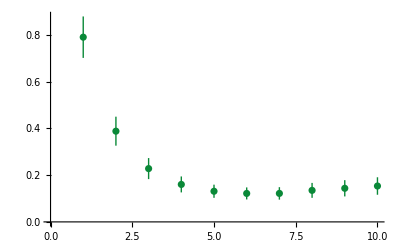

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]
```

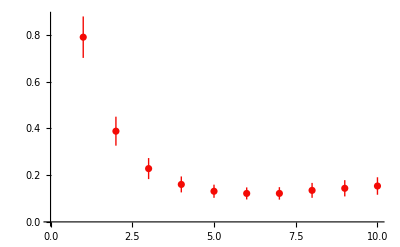

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]
```

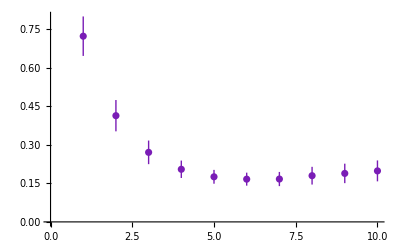

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]
```

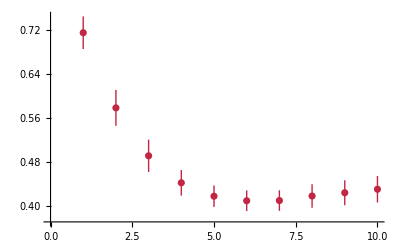

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]
```

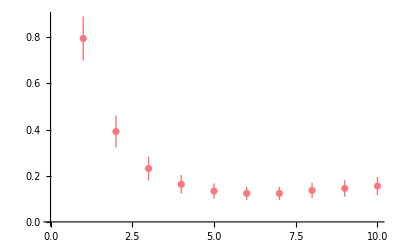

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]
```

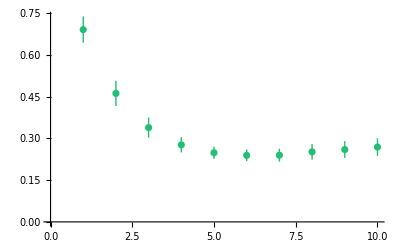

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]
```

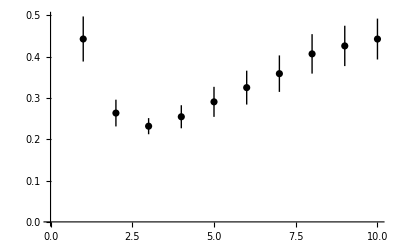

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->Black]
```

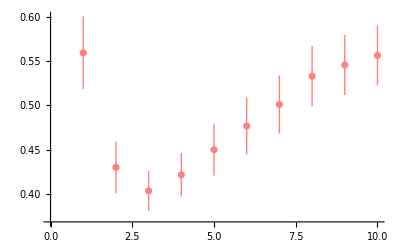

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->Pink]
```

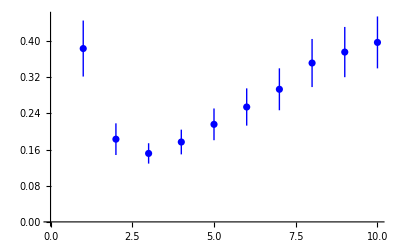

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}],PlotStyle->Blue]
```

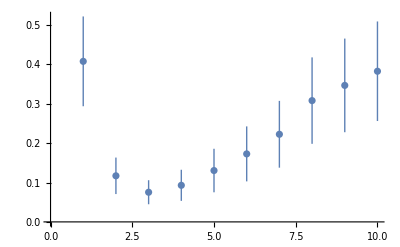

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}]]
```

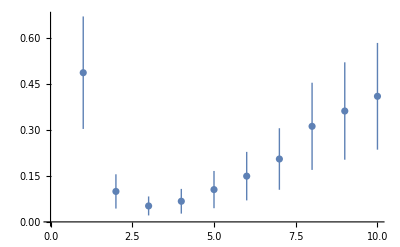

```mathematica
ListPlot[Table[100*Around[Table[aa[[x]][[y]],{x,100}]],{y,10}]]
```

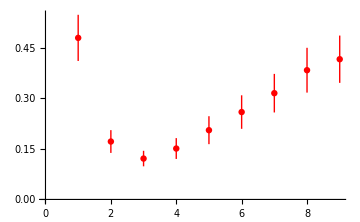

-Graphics-

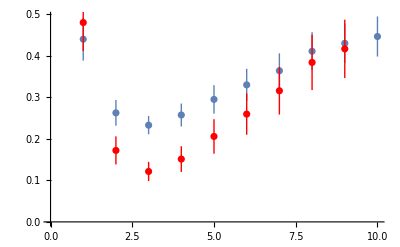

```mathematica
Show[%40,%41]
```

```mathematica
Clear[imp6,imp,imp3,imp,imp,imp,imp12,imp4,imp,imp13,imp12,imp5,imp,imp,imp7,imp,imp,imp,imp3,imp,imp4,imp7,imp,imp,imp11,imp,imp2,imp11,imp5,imp,imp,imp3,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp8,imp,imp1,imp,imp,imp10,imp,imp7,imp,imp,imp,imp9,imp4,imp,imp,imp,imp13,imp2,imp,imp,imp,imp,imp,imp,imp14,imp,imp11,imp,imp12,imp,imp,imp,imp,imp,imp14,imp1,imp,imp1,imp,imp6,imp,imp8,imp9,imp,imp,imp14,imp,imp13,imp10,imp2,imp6,imp8,imp9,imp]
```

```mathematica
RandomSample[Join[Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},7]],{imp,imp}]]
```

{imp8,imp8,imp6,imp5,imp12,imp7,imp9,imp14,imp4,imp8,imp11,imp11,imp14,imp6,imp12,imp14,imp12,imp2,imp6,imp10,imp7,imp1,imp3,imp10,imp6,imp8,imp13,imp10,imp,imp3,imp13,imp2,imp9,imp5,imp9,imp14,imp8,imp7,imp13,imp2,imp1,imp4,imp3,imp5,imp3,imp11,imp2,imp5,imp6,imp5,imp13,imp7,imp9,imp5,imp1,imp4,imp12,imp13,imp13,imp11,imp,imp8,imp10,imp1,imp13,imp3,imp6,imp2,imp12,imp4,imp4,imp10,imp5,imp14,imp14,imp2,imp11,imp2,imp10,imp3,imp14,imp9,imp12,imp7,imp1,imp4,imp7,imp11,imp7,imp6,imp1,imp1,imp9,imp10,imp8,imp11,imp12,imp9,imp3,imp4}